```mathematica
(*利用连续性来确定能量E*)
(*奇数次归一化条件为：B^2/k*Exp[-2*a*k]+A^2 a+A^2/2/q*Sin[2*q*a]==1*)
(*偶数次归一化条件为：D^2/k*Exp[-2*a*k]+C^2 a-C^2/2/q*Sin[2*q*a]==1*)
```

```mathematica
(*参数定义*)
m = 1;
V0 = 1;
a =3;
q=Sqrt[2*m*(V0 +e)];
k= Sqrt[2*m*(- e)];
```

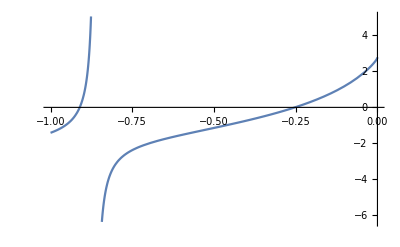

```mathematica
(*偶次能级*)
(*整个波函数必须满足连续性与连续可微性，即ψ'(x)/ψ(x)连续。
故有q*Tan[q*a]==k 
*)
(*先作图查看上面方程的根*)
f = q*Tan[q*a]-k;
Plot[f,{e,-1,0}]
```

```mathematica
(*找到两个根，列在下方*)
FindRoot[q*Tan[q*a]-k,{e,-0.9}]
```

{e→-0.910757}

```mathematica
FindRoot[q*Tan[q*a]==k,{e,-0.2}]
```

{e→-0.252509}

```mathematica
(*由归一化关系和连续性可得两个本征波函数*)
```

```mathematica
FindRoot[{B^2/k*Exp[-2*a*k]+A^2 a+A^2/2/q*Sin[2*q*a]==1 /.{e->-0.9107569241661659}, B Exp[-k a]==A Cos[q a]/.{e->-0.9107569241661659}},{{A,1},{B,1}}]
```

{A→0.517023,B→8.85551}

```mathematica
FindRoot[{B^2/k*Exp[-2*a*k]+A^2 a+A^2/2/q*Sin[2*q*a]==1 /.{e->-0.2525089824565585}, B Exp[-k a]==A Cos[q a]/.{e->-0.2525089824565585}},{{A,2},{B,3}}]
```

{A→0.476343,B→-3.47226}

```mathematica
(*所以可以列出偶次能级的两个本征波函数和本征能量*)
```

```mathematica
E1 = -0.9107569241661659
ψ1 = Piecewise[{{8.855509285993705Exp[k x],x<-a},{0.5170226357133262Cos[q x],-a<x<a},{8.855509285993705Exp[-k x],x>a}},x]/.{e->-0.9107569241661659}
```

-0.910757

Piecewise[{{8.85551 ⅇ^(1.34963 x), x<-3}, {0.517023 Cos[0.422476 x], -3<x<3}, {8.85551 ⅇ^(-1.34963 x), x>3}, {x, True}}]

```mathematica
E2 = -0.2525089824565585
ψ2= Piecewise[{{-3.472259720458546Exp[k x],x<-a},{0.4763433377842185Cos[q x],-a<x<a},{-3.472259720458546Exp[-k x],x>a}},x]/.{e->E2}
```

-0.252509

Piecewise[{{-3.47226 ⅇ^(0.710646 x), x<-3}, {0.476343 Cos[1.22269 x], -3<x<3}, {-3.47226 ⅇ^(-0.710646 x), x>3}, {x, True}}]

```mathematica
(*奇次能级*)
(*整个波函数必须满足连续性与连续可微性，即ψ'(x)/ψ(x)连续。
故有-q*Tan[q*a]==k 
*)
(*先作图查看上面方程的根*)
```

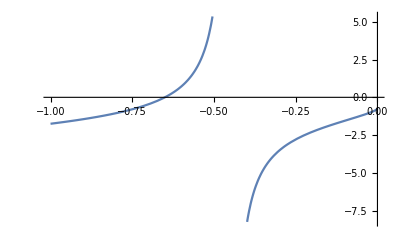

```mathematica
g = -q*Cot[q*a]-k;
Plot[g,{e,-1,0}]
```

```mathematica
(*找到一个根，列在下方*)
FindRoot[-q*Cot[q*a]-k,{e,-0.8}]
```

{e→-0.650311}

```mathematica
(*由归一化关系和连续性可得本征波函数*)
```

```mathematica
FindRoot[{d^2/k*Exp[-2*a*k]+c^2 a-c^2/2/q*Sin[2*q*a]==1 /.{e->-0.6503105289329637}, -d Exp[-k a]==c Sin[q a]/.{e->-0.6503105289329637}},{{d,2},{c,3}}]
```

{d→-9.19332,c→0.507879}

```mathematica
(*所以可以列出奇次能级的本征波函数和本征能量*)
```

```mathematica
E3 = -0.6503105289329637
ψ3= Piecewise[{{-9.193319314915835Exp[k x],x<-a},{0.5078793789347211Sin[q x],-a<x<a},{9.193319314915835Exp[-k x],x>a}},x]/.{e->E3}
```

-0.650311

Piecewise[{{-9.19332 ⅇ^(1.14045 x), x<-3}, {0.507879 Sin[0.836289 x], -3<x<3}, {9.19332 ⅇ^(-1.14045 x), x>3}, {x, True}}]

```mathematica
(*最后把上面三个波函数做在一个图里*)
```

```mathematica
Plot[{ψ1,ψ2,ψ3},{x,-5,5},AxesLabel->{"x","ψ(x)"},Prolog->Thickness[0.001],PlotRange->{-0.7,0.7},PlotLegends->"Expressions"]
```

-Graphics-